```mathematica
tuples=Tuples[{0,1},{3,3}];
n=Length[tuples];
side=Ceiling[Sqrt[n]];
padded=PadRight[tuples,{side^2,3,3}];
blocks=Partition[padded,side];
bigMatrix=ArrayFlatten[blocks];
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
fns=FileNames["t_*.mat","./"];
data=Import[#,"MAT"]&/@fns;
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
base=Import["../../CA/B3S236/base.mat","MAT"];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→False,./t_003.mat→False,./t_004.mat→False,./t_005.mat→False,./t_006.mat→False,./t_007.mat→False,./t_008.mat→False,./t_009.mat→False,./t_01.mat→False,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[6;;-5]]]]&/@Keys[datos];
```

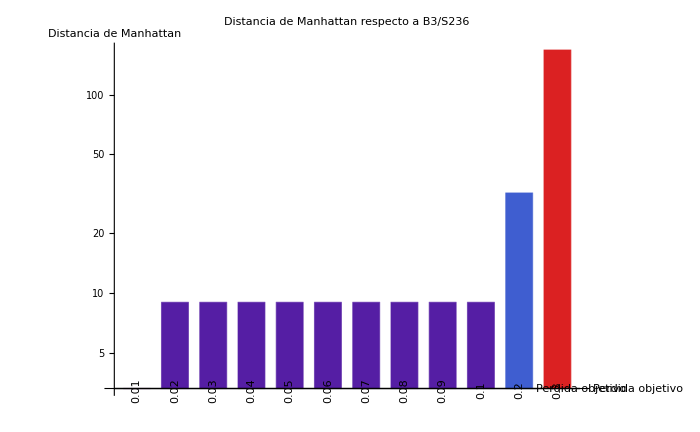

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S236",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../../Documentation/img/b3s236_loss.png",fplot];
```

```mathematica
Keys[datos]
```

{./t_00001.mat,./t_00002.mat,./t_00003.mat,./t_00004.mat,./t_00005.mat,./t_00006.mat,./t_00007.mat,./t_00008.mat,./t_00009.mat,./t_0001.mat,./t_0002.mat,./t_0003.mat,./t_0004.mat,./t_0005.mat,./t_0006.mat,./t_0007.mat,./t_0008.mat,./t_0009.mat,./t_001.mat,./t_002.mat,./t_003.mat,./t_004.mat,./t_005.mat,./t_006.mat,./t_007.mat,./t_008.mat,./t_009.mat,./t_01.mat,./t_02.mat,./t_03.mat}

```mathematica
Grid[{{ArrayPlot[data[[1,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-2,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]],
ArrayPlot[data[[-3,1,2]],Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]}}]
```

-Graphics-

```mathematica
ArrayPlot[vectors]
```

-Graphics-

```mathematica
ArrayPlot[vectors[[-3;;]],Mesh->True]
ArrayPlot[{vectors[[-1]]},Mesh->True]
ArrayPlot[{vectors[[-2]]},Mesh->True]
ArrayPlot[{vectors[[-3]]},Mesh->True]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
life=Import["../../CA/B3S23/base.mat","MAT"];
lifevector=Flatten[Part[life[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
life2=Import["../../CA/B3S238/base.mat","MAT"];
lifevector2=Flatten[Part[life2[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
fplotc=MatrixPlot[{
basevector[[-68;;-18]],
lifevector[[-68;;-18]],
vectors[[-2,-68;;-18]],
vectors[[-3,-68;;-18]],
vectors[[-4,-68;;-18]],
vectors[[-5,-68;;-18]],
vectors[[-6,-68;;-18]],
vectors[[-7,-68;;-18]],
vectors[[-8,-68;;-18]],
vectors[[-9,-68;;-18]],
vectors[[-10,-68;;-18]]
},FrameTicks->{{{{1,"B38/S238"},{2,"B3/S23"},{4,"NCA(0.2)"},{5,"NCA(0.1)"},{6,"NCA(0.09)"},{7,"NCA(0.08)"},{8,"NCA(0.07)"},{9,"NCA(0.06)"},{10,"NCA(0.05)"},{11,"NCA(0.04)"},{12,"NCA(0.03)"},{13,"NCA(0.02)"}},None},{None,None}},PlotLabel->"Comparación de vectores",ImagePadding->{{100,10},{30,30}},ImageSize->500,Mesh->True]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../../../Documentation/img/b38s238_vector.png",fplotc];
```

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-2]]],1]]
```

{128,192,224,248,252,254,255,320,352,376,380,382,383,384,416,440,444,446,447,472,476,478,479,480,500,502,503,504,506,507,509,511}

```mathematica
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-2,diff]]}];


Export["../../../../Documentation/img/b3s236_02_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/b3s236_02_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]]},Spacings->{0, 0}]]
```

{{{0,0,1},{1,1,1},{1,1,1}},{{0,1,0},{1,1,1},{1,1,1}},{{0,1,1},{0,1,1},{1,1,1}},{{0,1,1},{1,1,0},{1,1,1}},{{0,1,1},{1,1,1},{0,1,1}},{{0,1,1},{1,1,1},{1,0,1}},{{0,1,1},{1,1,1},{1,1,0}},{{1,0,0},{1,1,1},{1,1,1}},{{1,0,1},{0,1,1},{1,1,1}},{{1,0,1},{1,1,0},{1,1,1}},{{1,0,1},{1,1,1},{0,1,1}},{{1,0,1},{1,1,1},{1,0,1}},{{1,0,1},{1,1,1},{1,1,0}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{0,1,1},{1,1,1}},{{1,1,0},{1,1,0},{1,1,1}},{{1,1,0},{1,1,1},{0,1,1}},{{1,1,0},{1,1,1},{1,0,1}},{{1,1,0},{1,1,1},{1,1,0}},{{1,1,1},{0,1,0},{1,1,1}},{{1,1,1},{0,1,1},{0,1,1}},{{1,1,1},{0,1,1},{1,0,1}},{{1,1,1},{0,1,1},{1,1,0}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{0,1,1}},{{1,1,1},{1,1,0},{1,0,1}},{{1,1,1},{1,1,0},{1,1,0}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,0,1}},{{1,1,1},{1,1,1},{0,1,0}},{{1,1,1},{1,1,1},{1,0,0}},{{1,1,1},{1,1,1},{1,1,0}}}

../../../../Documentation/img/b3s236_02_10.png

../../../../Documentation/img/b3s236_02_01.png

```mathematica
diff=Flatten[Position[Abs[basevector-vectors[[-3]]],1]]
diftuples=tuples[[diff]]
dif2=Transpose[{basevector[[diff]],vectors[[-3,diff]]}]
```

{256,384,448,480,504,508,510,511,512}

{{{0,1,1},{1,1,1},{1,1,1}},{{1,0,1},{1,1,1},{1,1,1}},{{1,1,0},{1,1,1},{1,1,1}},{{1,1,1},{0,1,1},{1,1,1}},{{1,1,1},{1,1,0},{1,1,1}},{{1,1,1},{1,1,1},{0,1,1}},{{1,1,1},{1,1,1},{1,0,1}},{{1,1,1},{1,1,1},{1,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}

{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

```mathematica
Export["../../../../Documentation/img/b3s236_03_10.png",Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{0,1}]]]],4
],Spacings->{0, 0}]]
Export["../../../../Documentation/img/b3s236_03_01.png",
Grid[{ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2[[-1;;-1]],{0,1}]]]]},Spacings->{0, 0}]]
```

../../../../Documentation/img/b3s236_03_10.png

../../../../Documentation/img/b3s236_03_01.png

```mathematica
Grid[Partition[
ArrayPlot[#,Mesh->True,ImageSize->40]&/@diftuples[[Flatten[Position[dif2,{1,0}]]]],UpTo[6]
],Spacings->{0, 0}]
```